```mathematica
ClearAll;
Rx = 1/(√2)*({{√2, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, √2, 0, 0}, {0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, -1, 0}});
z6 = ConstantArray[0,{6,6}];
z3 = ConstantArray[0,{3,3}];
Δ = 1;
w=1/40;
k=w *Δ;
```

```mathematica
Rx78 = ConstantArray[0,{78,78}];
For[i=1,i<78,i=i+6,Rx78[[i;;i+5,i;;i+5]]=Rx];
(*Rx78 // MatrixForm*)
```

```mathematica
adagQx= Transpose[Rx78].DiagonalMatrix[{0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1}].Rx78;
adagQx[[1;;18, 1;;18]] = IdentityMatrix[18];
adagQx[[61;;78, 61;;78]] = IdentityMatrix[18];
(*adagQx // MatrixForm*)
```

```mathematica
StencilP=1/Δ *{-1/12, 1/2, -3/2, 5/6, 1/4, 0, 0};
StencilM =1/Δ *{0,0,-1/4,-5/6,3/2,-1/2,-1/12 };
SvUpper= ArrayReshape[{Transpose[{IdentityMatrix[3],z3}],Transpose[{z3, z3}]},{6,6}];
SvLower = ArrayReshape[{Transpose[{z3,z3}],Transpose[{z3, IdentityMatrix[3]}]},{6,6}];
Sv =ConstantArray[0,{78,78}]; 
Sv[[1;;18, 1;;18]] = IdentityMatrix[18];
Sv[[61;;78, 61;;78]] = IdentityMatrix[18];
For[i=3,i<10,i=i+1,For[j=0+i-3,j<7+i-3,j=j+1,Sv[[i*6+1;;i*6+5+1,j*6+1;;j*6+5+1]]=SvUpper*StencilM[[j+4-i]] + SvLower*StencilP[[j+4-i]]]]
(*MatrixForm[Sv]*)
```

{0,0,ⅇ^(ⅈ (t/40+(6-x)/40)),0,-ⅇ^(ⅈ (t/40+(6-x)/40)),0,0,0,ⅇ^(ⅈ (t/40+(5-x)/40)),0,-ⅇ^(ⅈ (t/40+(5-x)/40)),0,0,0,ⅇ^(ⅈ (t/40+(4-x)/40)),0,-ⅇ^(ⅈ (t/40+(4-x)/40)),0,0,0,10000 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+1460000/3 ⅇ^(ⅈ (t/40+(1-x)/40))-2120000/27 ⅇ^(ⅈ (t/40+(2-x)/40))-144350000/81 ⅇ^(ⅈ (t/40+(3-x)/40))+(14876200/9+(52820 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))-(13257100/27+7980 ⅈ) ⅇ^(ⅈ (t/40+(5-x)/40))+(5669000/81+(45910 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))+400000/3 ⅇ^(ⅈ (t/40-x/40)),0,-10000 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-1460000/3 ⅇ^(ⅈ (t/40+(1-x)/40))+2120000/27 ⅇ^(ⅈ (t/40+(2-x)/40))+144350000/81 ⅇ^(ⅈ (t/40+(3-x)/40))-(14876200/9+(52820 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))+(13257100/27+7980 ⅈ) ⅇ^(ⅈ (t/40+(5-x)/40))-(5669000/81+(45910 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))-400000/3 ⅇ^(ⅈ (t/40-x/40)),0,0,0,10000 ⅇ^(ⅈ (t/40+1/40 (-2-x)))+400000/3 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-23180000/27 ⅇ^(ⅈ (t/40+(1-x)/40))-359540000/81 ⅇ^(ⅈ (t/40+(2-x)/40))+1400000 ⅇ^(ⅈ (t/40+(3-x)/40))+(131365700/27-223980 ⅈ) ⅇ^(ⅈ (t/40+(4-x)/40))-(154073800/81-(2043910 ⅈ)/27) ⅇ^(ⅈ (t/40+(5-x)/40))+(3248200/9-(38000 ⅈ)/3) ⅇ^(ⅈ (t/40+(6-x)/40))+1280000/3 ⅇ^(ⅈ (t/40-x/40)),0,-10000 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-400000/3 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+23180000/27 ⅇ^(ⅈ (t/40+(1-x)/40))+359540000/81 ⅇ^(ⅈ (t/40+(2-x)/40))-1400000 ⅇ^(ⅈ (t/40+(3-x)/40))-(131365700/27-223980 ⅈ) ⅇ^(ⅈ (t/40+(4-x)/40))+(154073800/81-(2043910 ⅈ)/27) ⅇ^(ⅈ (t/40+(5-x)/40))-(3248200/9-(38000 ⅈ)/3) ⅇ^(ⅈ (t/40+(6-x)/40))-1280000/3 ⅇ^(ⅈ (t/40-x/40)),0,0,0,10000 ⅇ^(ⅈ (t/40+1/40 (-3-x)))+400000/3 ⅇ^(ⅈ (t/40+1/40 (-2-x)))+1280000/3 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-309050000/81 ⅇ^(ⅈ (t/40+(1-x)/40))+62000000/9 ⅇ^(ⅈ (t/40+(2-x)/40))+380180000/27 ⅇ^(ⅈ (t/40+(3-x)/40))-(1888456600/81-(9873910 ⅈ)/27) ⅇ^(ⅈ (t/40+(4-x)/40))+(69134600/9-110000 ⅈ) ⅇ^(ⅈ (t/40+(5-x)/40))-(11259400/9-(49000 ⅈ)/3) ⅇ^(ⅈ (t/40+(6-x)/40))-22640000/27 ⅇ^(ⅈ (t/40-x/40)),0,-10000 ⅇ^(ⅈ (t/40+1/40 (-3-x)))-400000/3 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-1280000/3 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+309050000/81 ⅇ^(ⅈ (t/40+(1-x)/40))-62000000/9 ⅇ^(ⅈ (t/40+(2-x)/40))-380180000/27 ⅇ^(ⅈ (t/40+(3-x)/40))+(1888456600/81-(9873910 ⅈ)/27) ⅇ^(ⅈ (t/40+(4-x)/40))-(69134600/9-110000 ⅈ) ⅇ^(ⅈ (t/40+(5-x)/40))+(11259400/9-(49000 ⅈ)/3) ⅇ^(ⅈ (t/40+(6-x)/40))+22640000/27 ⅇ^(ⅈ (t/40-x/40)),0,0,0,10000 ⅇ^(ⅈ (t/40+1/40 (-4-x)))+400000/3 ⅇ^(ⅈ (t/40+1/40 (-3-x)))+1280000/3 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-22640000/27 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+59440000/9 ⅇ^(ⅈ (t/40+(1-x)/40))+234320000/27 ⅇ^(ⅈ (t/40+(2-x)/40))-2974360000/81 ⅇ^(ⅈ (t/40+(3-x)/40))+(102607600/3-(800000 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))-(91638800/9-(206000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))+(40599700/27-(236000 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))-309320000/81 ⅇ^(ⅈ (t/40-x/40)),0,-10000 ⅇ^(ⅈ (t/40+1/40 (-4-x)))-400000/3 ⅇ^(ⅈ (t/40+1/40 (-3-x)))-1280000/3 ⅇ^(ⅈ (t/40+1/40 (-2-x)))+22640000/27 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-59440000/9 ⅇ^(ⅈ (t/40+(1-x)/40))-234320000/27 ⅇ^(ⅈ (t/40+(2-x)/40))+2974360000/81 ⅇ^(ⅈ (t/40+(3-x)/40))-(102607600/3-(800000 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))+(91638800/9-(206000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))-(40599700/27-(236000 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))+309320000/81 ⅇ^(ⅈ (t/40-x/40)),0,0,0,(100000-1000 ⅈ) ⅇ^(ⅈ (t/40+1/40 (-4-x)))+1460000/3 ⅇ^(ⅈ (t/40+1/40 (-3-x)))-23180000/27 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-309050000/81 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+236480000/27 ⅇ^(ⅈ (t/40+(1-x)/40))-2715160000/81 ⅇ^(ⅈ (t/40+(2-x)/40))+391510000/9 ⅇ^(ⅈ (t/40+(3-x)/40))-(248598800/9-(350000 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))+(198279700/27-(668000 ⅈ)/27) ⅇ^(ⅈ (t/40+(5-x)/40))-(8800000/9-(8000 ⅈ)/3) ⅇ^(ⅈ (t/40+(6-x)/40))+59440000/9 ⅇ^(ⅈ (t/40-x/40)),0,(-100000+1000 ⅈ) ⅇ^(ⅈ (t/40+1/40 (-4-x)))-1460000/3 ⅇ^(ⅈ (t/40+1/40 (-3-x)))+23180000/27 ⅇ^(ⅈ (t/40+1/40 (-2-x)))+309050000/81 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-236480000/27 ⅇ^(ⅈ (t/40+(1-x)/40))+2715160000/81 ⅇ^(ⅈ (t/40+(2-x)/40))-391510000/9 ⅇ^(ⅈ (t/40+(3-x)/40))+(248598800/9-(350000 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))-(198279700/27-(668000 ⅈ)/27) ⅇ^(ⅈ (t/40+(5-x)/40))+(8800000/9-(8000 ⅈ)/3) ⅇ^(ⅈ (t/40+(6-x)/40))-59440000/9 ⅇ^(ⅈ (t/40-x/40)),0,0,0,(639700/3-(20000 ⅈ)/3) ⅇ^(ⅈ (t/40+1/40 (-4-x)))-2120000/27 ⅇ^(ⅈ (t/40+1/40 (-3-x)))-359540000/81 ⅇ^(ⅈ (t/40+1/40 (-2-x)))+62000000/9 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-2715160000/81 ⅇ^(ⅈ (t/40+(1-x)/40))+380200000/9 ⅇ^(ⅈ (t/40+(2-x)/40))-852640000/27 ⅇ^(ⅈ (t/40+(3-x)/40))+(393759700/27-(884000 ⅈ)/27) ⅇ^(ⅈ (t/40+(4-x)/40))-(30560000/9-(16000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))+(10900000/27-(4000 ⅈ)/9) ⅇ^(ⅈ (t/40+(6-x)/40))+234320000/27 ⅇ^(ⅈ (t/40-x/40)),0,(-639700/3+(20000 ⅈ)/3) ⅇ^(ⅈ (t/40+1/40 (-4-x)))+2120000/27 ⅇ^(ⅈ (t/40+1/40 (-3-x)))+359540000/81 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-62000000/9 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+2715160000/81 ⅇ^(ⅈ (t/40+(1-x)/40))-380200000/9 ⅇ^(ⅈ (t/40+(2-x)/40))+852640000/27 ⅇ^(ⅈ (t/40+(3-x)/40))-(393759700/27-(884000 ⅈ)/27) ⅇ^(ⅈ (t/40+(4-x)/40))+(30560000/9-(16000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))-(10900000/27-(4000 ⅈ)/9) ⅇ^(ⅈ (t/40+(6-x)/40))-234320000/27 ⅇ^(ⅈ (t/40-x/40)),0,0,0,(-5669000/27-(45910 ⅈ)/9) ⅇ^(ⅈ (t/40+1/40 (-4-x)))-144350000/81 ⅇ^(ⅈ (t/40+1/40 (-3-x)))+1400000 ⅇ^(ⅈ (t/40+1/40 (-2-x)))+380180000/27 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+391510000/9 ⅇ^(ⅈ (t/40+(1-x)/40))-852640000/27 ⅇ^(ⅈ (t/40+(2-x)/40))+425000000/27 ⅇ^(ⅈ (t/40+(3-x)/40))-(16160000/3-6000 ⅈ) ⅇ^(ⅈ (t/40+(4-x)/40))+(28780000/27-(2000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))-(2980000/27-(1000 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))-2974360000/81 ⅇ^(ⅈ (t/40-x/40)),0,(5669000/27+(45910 ⅈ)/9) ⅇ^(ⅈ (t/40+1/40 (-4-x)))+144350000/81 ⅇ^(ⅈ (t/40+1/40 (-3-x)))-1400000 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-380180000/27 ⅇ^(ⅈ (t/40+1/40 (-1-x)))-391510000/9 ⅇ^(ⅈ (t/40+(1-x)/40))+852640000/27 ⅇ^(ⅈ (t/40+(2-x)/40))-425000000/27 ⅇ^(ⅈ (t/40+(3-x)/40))+(16160000/3-6000 ⅈ) ⅇ^(ⅈ (t/40+(4-x)/40))-(28780000/27-(2000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))+(2980000/27-(1000 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))+2974360000/81 ⅇ^(ⅈ (t/40-x/40)),0,0,0,ⅇ^(ⅈ (t/40+1/40 (-4-x))),0,-ⅇ^(ⅈ (t/40+1/40 (-4-x))),0,0,0,ⅇ^(ⅈ (t/40+1/40 (-5-x))),0,-ⅇ^(ⅈ (t/40+1/40 (-5-x))),0,0,0,ⅇ^(ⅈ (t/40+1/40 (-6-x))),0,-ⅇ^(ⅈ (t/40+1/40 (-6-x))),0}

Re[10000 ⅇ^(ⅈ (t/40+1/40 (-4-x)))+400000/3 ⅇ^(ⅈ (t/40+1/40 (-3-x)))+1280000/3 ⅇ^(ⅈ (t/40+1/40 (-2-x)))-22640000/27 ⅇ^(ⅈ (t/40+1/40 (-1-x)))+59440000/9 ⅇ^(ⅈ (t/40+(1-x)/40))+234320000/27 ⅇ^(ⅈ (t/40+(2-x)/40))-2974360000/81 ⅇ^(ⅈ (t/40+(3-x)/40))+(102607600/3-(800000 ⅈ)/3) ⅇ^(ⅈ (t/40+(4-x)/40))-(91638800/9-(206000 ⅈ)/3) ⅇ^(ⅈ (t/40+(5-x)/40))+(40599700/27-(236000 ⅈ)/27) ⅇ^(ⅈ (t/40+(6-x)/40))-309320000/81 ⅇ^(ⅈ (t/40-x/40))]

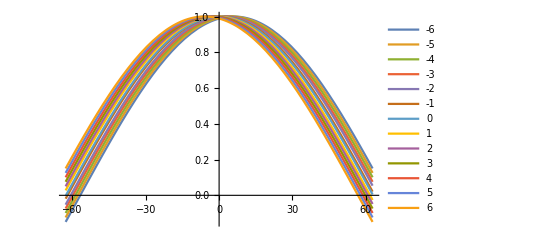

```mathematica
step =adagQx.Transpose[Rx78].Sv.Rx78 ;
(*Eigenvalues[step]*)
step // MatrixForm;
f=Table[0,78];

intMat = -ⅈ/(w*Δ)*IdentityMatrix[78];
intMat[[1;;18, 1;;18]] = IdentityMatrix[18];
intMat[[61;;78, 61;;78]] =IdentityMatrix[18];

For[i=1,i<78, i = i+6, f[[i+2]]=Exp[ⅈ(Δ*w*t -k(x+((i-1)/6 -6)Δ))]];
For[i=1,i<78, i = i+6, f[[i+4]]=-Exp[ⅈ(Δ*w*t -k(x+((i-1)/6 -6)Δ))]] ;
out =intMat.step.intMat.step.intMat.step.intMat.step.f (*Only integrate the values, that get derived*)
g[x_, t_] = Re[out[[3]]];
h[x_, t_] = Re[out[[9]]];
l[x_, t_] = Re[out[[15]]];

m[x_, t_] = Re[out[[21]]];
n[x_, t_] = Re[out[[27]]];
o[x_, t_] = Re[out[[33]]];
p[x_, t_] = Re[out[[39]]]
q[x_, t_] = Re[out[[45]]];
r[x_, t_] = Re[out[[51]]];
s[x_, t_] = Re[out[[57]]];

u[x_, t_] = Re[out[[63]]];
v[x_, t_] = Re[out[[69]]];
a[x_, t_] = Re[out[[75]]];

With[{t=0},Plot[{g[x,t],h[x,t],l[x,t],m[x,t],n[x,t],o[x,t],p[x,t],q[x,t],r[x,t],s[x,t],u[x,t],v[x,t],a[x,t]},{x, -3.14*20,3.14*20},PlotLegends->{"-6","-5","-4","-3","-2","-1","0","1","2","3","4","5","6"}]]
```